```mathematica
ComplexPlot3D[Gamma[z],{z,-10-10I,7+7I},PlotLegends->Automatic,ImageSize->Full]
```

-Graphics3D-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"Gamma Function plotted in the complex plane in three dimensions with Mathematica ComplexPlot3D.svg"}],ComplexPlot3D[Gamma[z],{z,-10-10I,7+7I},PlotLegends->Automatic,ImageSize->Full]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\Gamma Function plotted in the complex plane in three dimensions with Mathematica ComplexPlot3D.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\Gamma Function plotted in the complex plane in three dimensions with Mathematica ComplexPlot3D.svg"]
```

```mathematica
ComplexPlot3D[Gamma[z],{z,-7-2ⅈ,9+7I},PlotLegends->Automatic,ImageSize->Large,PlotRange->{0,4}]
```

-Graphics3D-

```mathematica
?ComplexPlot3D
```

```mathematica
FunctionPoles[Gamma[x],x]
```

{{ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≤0],1},{ConditionalExpression[1+2 C[1], C[1]∈ℤ&&C[1]≤-1],1}}

```mathematica
First[FunctionPoles[Gamma[x],x]]
```

{ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≤0],1}

```mathematica
First[First[FunctionPoles[Gamma[x],x]]]
```

ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≤0]

```mathematica
FindInstance[First[First[FunctionPoles[Gamma[x],x]]],C[1]]
```

FindInstance::naqs: 1∈&&1≤0&&2 1 is not a quantified system of equations and inequalities.

FindInstance[ConditionalExpression[2 C[1], C[1]∈ℤ&&C[1]≤0],C[1]]

```mathematica
ComplexPlot3D[Gamma[z],{z,7-2ⅈ,12+7I},PlotLegends->Automatic,ImageSize->Large,PlotRange->{0,10^7}]
```

-Graphics3D-

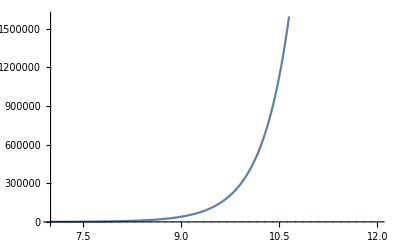

```mathematica
ReImPlot[Gamma[z],{z,7,12}]
```

```mathematica
AbsArgPlot[Gamma[z],{z,-4,7}]
```

-Graphics-

```mathematica
AbsArgPlot[Gamma[z],{z,-4,7},ImageSize->Full]
```

-Graphics-

```mathematica
AbsArgPlot[Gamma[z],{z,-4,7},ImageSize->Full,PlotLegends->Automatic]
```

-Graphics-

```mathematica
AbsArgPlot[Gamma[z],{z,-4,7},ImageSize->Full,PlotLegends->Automatic,Filling->Bottom]
```

-Graphics-

```mathematica
ComplexPlot[Gamma[z],{z,-2-2I,2+2I},PlotLegends->Automatic]
```

-Graphics-

```mathematica
ComplexPlot[Gamma[z],{z,-2-2I,2+2I},PlotLegends->Automatic,PlotTheme->"Business"]
```

-Graphics-

```mathematica
ComplexPlot[Gamma[z],{z,-2-2I,2+2I},PlotLegends->Automatic,ImageSize->Full]
```

-Graphics-

```mathematica
ComplexPlot[Gamma[z],{z,-2-2I,6+2I},PlotLegends->Automatic,ImageSize->Full]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot of gamma function in the complex plane from -2-i to 6+2i with colors created in Mathematica.svg"}],ComplexPlot[Gamma[z],{z,-2-2I,6+2I},PlotLegends->Automatic,ImageSize->Full]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\plot of gamma function in the complex plane from -2-i to 6+2i with colors created in Mathematica.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\plot of gamma function in the complex plane from -2-i to 6+2i with colors created in Mathematica.svg"]
```

```mathematica
AbsArgPlot[Gamma[z],{z,-4,7},ImageSize->Full,PlotLegends->Automatic]
```

-Graphics-

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"absolute argument plot of the gamma function from z=-4 to 7 created in Mathematica 13.1.svg"}],AbsArgPlot[Gamma[z],{z,-4,7},ImageSize->Full,PlotLegends->Automatic]]
```

C:\Users\peter\Documents\GitHub\data-visualization-functions\absolute argument plot of the gamma function from z=-4 to 7 created in Mathematica 13.1.svg

```mathematica
SystemOpen["C:\\Users\\peter\\Documents\\GitHub\\data-visualization-functions\\absolute argument plot of the gamma function from z=-4 to 7 created in Mathematica 13.1.svg"]
```